# Chemical Bonds: Molecular Orbitals for One-Electron Diatomic Molecules

Mohammad Alhudaithi

Mentor : Mohammad Bahrami

## Introduction

Molecular Orbital (MO) theory is among the fundamental models describing molecular structure. Chemical reactivity highly depends on two features of MO: the probability distribution, and corresponding energy levels. The goal of this project is to calculate these features for different combinations of atomic orbitals of one-electron diatomic molecules as a function of internuclear distance.

## Defining the hydrogen wave function

The first step is to define a function that takes quantum numbers as its input, and outputs the appropriate wave function. This was made easier by using built in functions.

Generates atomic wave function with variables n, l, ml, and electron position in spherical coordinates

```mathematica
ψ[n_,l_,m_][r_,θ_,ϕ_]:=√(((n-l-1)!)/((n+l)!)) ⅇ^(-r/(n)) ((2r)/n)^l 2/n^2 LaguerreL[n-l-1,2 l+1,(2 r)/n] SphericalHarmonicY[l,m,θ,ϕ];
```

This is where I encountered my first hurdle, the function takes spherical coordinates but all the functions Mathematic uses for 3D graphs accept Cartesian coordinates. To get around this problem, I used a function to convert Cartesian coordinates to spherical coordinates.

Converts Cartesian coordinates to spherical coordinates

```mathematica
sphericalToCartesian=Thread[{r,θ,ϕ}->{Sqrt[x^2+y^2+z^2],ArcCos[z/Sqrt[x^2+y^2+z^2]],Arg[x+ⅈ y]}];
```

## Graphing Unhybridized Atomic Orbitals

Using the wave function and region plot I graphed some atomic orbitals to see what they look like.

Graphs the 1S orbital using the wave function

```mathematica
S1=RegionPlot3D[Evaluate[Abs[ψ[1,0,0][r,θ,ϕ]]^2/.sphericalToCartesian]>.01/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->LightBlue]
```

-Graphics3D-

Graphs the 2S orbital

```mathematica
S2=RegionPlot3D[Evaluate[Abs[ψ[2,0,0][r,θ,ϕ]]^2/.sphericalToCartesian]>.01/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->LightBlue]
```

-Graphics3D-

Graphs the 2Pz orbital

```mathematica
Pz=RegionPlot3D[Evaluate[Abs[ψ[2,1,0][r,θ,ϕ]]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

This is where I encountered the second issue. The Pz orbitals is the usual dumbbell shape, but the other P orbitals look different.

Graphs the first complex solution of the 2P Orbital

```mathematica
complex1 = RegionPlot3D[Evaluate[Abs[ψ[2,1,1][r,θ,ϕ]]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->LightBlue]
```

-Graphics3D-

Graphs the second complex solution of the 2P orbital

```mathematica
complex2=RegionPlot3D[Evaluate[Abs[ψ[2,1,-1][r,θ,ϕ]]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->LightBlue]
```

-Graphics3D-

I found out that the wave function outputs complex solutions for l=-1,1. To get the Px and Py orbitals, I added and subtracted the complex solutions respectively.

Graphs the Px Orbital

```mathematica
Px=RegionPlot3D[Evaluate[Abs[-1/(√2)(ψ[2,1,1][r,θ,ϕ]-ψ[2,1,-1][r,θ,ϕ])]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

Graphs the Py Orbital

```mathematica
Py=RegionPlot3D[Evaluate[Abs[ⅈ/(√2)(ψ[2,1,1][r,θ,ϕ]+ψ[2,1,-1][r,θ,ϕ])]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

## Graphing Hybrid Atomic Orbitals

### SP hybridized atoms

Graphing hybrid orbitals is done by combining the constituent orbital in different ways. You may notice the opacity manually set to one, this is to make it easier to change later.

Linear addition of S and Pz orbitals to obtain an SP hybrid orbital

```mathematica
SP11=RegionPlot3D[Evaluate[Abs[1/(√2)(ψ[2,0,0][r,θ,ϕ]+ψ[2,1,0][r,θ,ϕ])]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

Linear subtraction to obtain the other SP orbital

```mathematica
SP12=RegionPlot3D[Evaluate[Abs[1/(√2)(ψ[2,0,0][r,θ,ϕ]-ψ[2,1,0][r,θ,ϕ])]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

In order to see the geometric structure of an atom of a specific hybridization state, I used the show function to superimpose the orbitals and decreased the opacity to make the structure clearer. This graph explains the linear nature of SP hybridized atoms in molecules like acetylene.

Using show to overlay the Px, Py, and the two SP orbitals and decreasing the opacity to make it easier to see

```mathematica
Show[{SP11,SP12,Px,Py}/.Opacity[1]->Opacity[0.5]]
```

-Graphics3D-

### SP2 hybridized atoms

Graphing an SP2 orbital using a linear combination of the 2S and 2Px orbitals

```mathematica
SP21=RegionPlot3D[Evaluate[Abs[1/√3*(ψ[2,0,0][r,θ,ϕ]+√2*ⅈ/(√2)(ψ[2,1,1][r,θ,ϕ]+ψ[2,1,-1][r,θ,ϕ]))]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

Graphing the SP2 Orbital using a linear combination of the 2S, 2Px, and 2Py

```mathematica
SP22=RegionPlot3D[Evaluate[Abs[1/√3*(ψ[2,0,0][r,θ,ϕ]+√(3/2)*-1/(√2)(ψ[2,1,1][r,θ,ϕ]-ψ[2,1,-1][r,θ,ϕ])-√0.5*ⅈ/(√2)(ψ[2,1,1][r,θ,ϕ]+ψ[2,1,-1][r,θ,ϕ]))]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

Graphing the SP2 Orbital using a linear combination of the 2S, 2Px, and 2Py

```mathematica
SP23=RegionPlot3D[Evaluate[Abs[1/√3*(ψ[2,0,0][r,θ,ϕ]-√(3/2)*-1/(√2)(ψ[2,1,1][r,θ,ϕ]-ψ[2,1,-1][r,θ,ϕ])-√0.5*ⅈ/(√2)(ψ[2,1,1][r,θ,ϕ]+ψ[2,1,-1][r,θ,ϕ]))]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

This graph showcases the trigonal planar shape of SP2 hybridized atoms.

Overlaying the SP2 and Pz Orbitals and decreasing the opacity to obtain a clearer image

```mathematica
Show[{SP21,SP22,SP23,Pz}/.Opacity[1]->Opacity[0.5]/.LightBlue->LightBlue]
```

-Graphics3D-

### SP3 hybridized atoms

Graphing an SP3 orbital

```mathematica
SP31 = RegionPlot3D[Evaluate[Abs[0.5(ψ[2,0,0][r,θ,ϕ]+-1/(√2)(ψ[2,1,1][r,θ,ϕ]-ψ[2,1,-1][r,θ,ϕ])+ⅈ/(√2)(ψ[2,1,1][r,θ,ϕ]+ψ[2,1,-1][r,θ,ϕ])+ψ[2,1,0][r,θ,ϕ])]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

Graphing an SP3 hybridized orbital

```mathematica
SP32=RegionPlot3D[Evaluate[Abs[0.5(ψ[2,0,0][r,θ,ϕ]--1/(√2)(ψ[2,1,1][r,θ,ϕ]-ψ[2,1,-1][r,θ,ϕ])-ⅈ/(√2)(ψ[2,1,1][r,θ,ϕ]+ψ[2,1,-1][r,θ,ϕ])+ψ[2,1,0][r,θ,ϕ])]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

Graphing an SP3 orbital

```mathematica
SP33=RegionPlot3D[Evaluate[Abs[0.5(ψ[2,0,0][r,θ,ϕ]--1/(√2)(ψ[2,1,1][r,θ,ϕ]-ψ[2,1,-1][r,θ,ϕ])+ⅈ/(√2)(ψ[2,1,1][r,θ,ϕ]+ψ[2,1,-1][r,θ,ϕ])-ψ[2,1,0][r,θ,ϕ])]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

Graphing an SP3 orbital

```mathematica
SP34=RegionPlot3D[Evaluate[Abs[0.5(ψ[2,0,0][r,θ,ϕ]+-1/(√2)(ψ[2,1,1][r,θ,ϕ]-ψ[2,1,-1][r,θ,ϕ])-ⅈ/(√2)(ψ[2,1,1][r,θ,ϕ]+ψ[2,1,-1][r,θ,ϕ])-ψ[2,1,0][r,θ,ϕ])]^2/.sphericalToCartesian]>.043/2^6,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic,Mesh->False,PlotPoints->30,PlotStyle->Directive[LightBlue,Opacity[1]]]
```

-Graphics3D-

This graph showcases the tetrahedral shape of SP3 hybridized atoms.

Overlaying the  orbitals and decreasing the opacity

```mathematica
Show[{SP31,SP32,SP33,SP34}/.Opacity[1]->Opacity[0.5]]
```

-Graphics3D-

### Examining S and P character of hybrid orbitals

```mathematica
GraphicsRow[{SP11,SP22,SP31},ImageSize->Full]
```

-Graphics-

An interesting quality of hybrid orbitals is the percent character of each constituent orbital. An SP orbital has 50% S character and 50% P character, n SP2 orbital has 33% S character and 67% P character, and an SP3 orbital has 25% S character and 75% P character. The percent character of an orbital changes the overall shape of the resulting hybrid orbital. In the graphs above, you can clearly see the orbitals start to resemble P orbitals more and more as the P character increases, and resemble S orbitals less and less as S character decreases.

## Molecular orbitals

### Computing distance/energy data

To compute the energy of a molecular orbital at a specific distance, I implemented functions to calculate the overlap, Coulomb, and resonance integrals.

Defining a function for the solution of the overlap integral

```mathematica
s[R_]:=(ⅇ^(-(R Z)/a0) (3 a0^2+3 a0 R Z+R^2 Z^2))/(3 a0^2);
```

Defining a function for the solution of the Coulomb integral

```mathematica
α [R_]:= E1s -j0/R(1-(1+(Z R)/a0)Exp[-2(Z R)/a0])+j0/R;
```

Another issue I faced while calculating β is that the output included a conditional statement. To get around this problem, I used the simplify function with a condition.

Defining a function for the solution of the resonance integral

```mathematica
β[R_]:=Simplify[(E1s+j0/R)*s[R]-j0/a0(1+R/a0)Exp[-R/a0],Assumptions->R>0];
```

Defining the constant j_0 with the appropriate SI units

```mathematica
j0=QuantityMagnitude@UnitConvert[(Quantity[, "ElementaryCharge"])^2/(4π*Quantity[, "ElectricConstant"]),"Joules""Meters"];
```

Calculating the energy of the 1s orbital with the appropriate SI units using the Bohr approximation

```mathematica
E1s=-QuantityMagnitude@UnitConvert[(Entity["Particle","Electron"][EntityProperty["Particle","Mass"]]*Entity["Particle","Electron"][EntityProperty["Particle","Charge"]]^4)/(2(4π*Quantity[, "ElectricConstant"])^2*(Quantity[, "PlanckConstant"]/(2π))^2),"Joules"];
```

Converting the Bohr radius to meters

```mathematica
a0=QuantityMagnitude@UnitConvert[Quantity[1, "BohrRadius"],"Meters"];
```

Defining conditions for calculations

```mathematica
distanceL =10^-11;
distanceH= 5*10^-10;
step= 10^-12;
```

Here, I used the integrals I defined in the solution of the Hamiltonian to compute the energy of the orbital as a function of the internuclear distance.

Calculating the energy of the bonding orbital for the defined distances

```mathematica
addition = Table[{R,(α[R]+β[R])/(1+s[R])/.{Z->1}},{R,distanceL,distanceH,step}];
```

Calculating the energy of the antibonding orbital for the defined distances

```mathematica
subtraction= Table[{R,(α[R]-β[R])/(1-s[R])/.{Z->1}},{R,distanceL,distanceH,step}];
```

Setting the energy of atoms at infinite distance to be zero and converting units

```mathematica
normalizedData=Association[#1/a0->(1-#2/E1s)&@@@addition];
```

```mathematica
normalizedData2=Association[#1/a0->(1-#2/E1s)&@@@subtraction];
```

### Visualizing data

Plotting the data in a graph

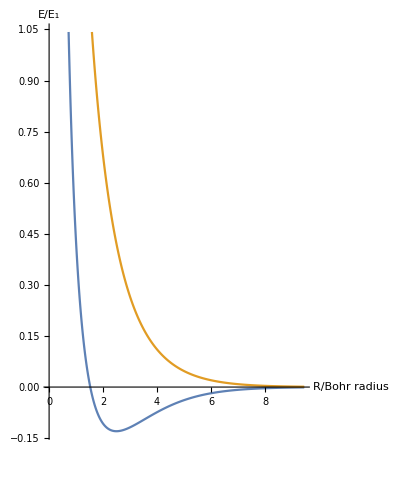

```mathematica
ListLinePlot[{normalizedData,normalizedData2},AxesLabel->{"R/Bohr radius","E/E_1"},AspectRatio->1.2]
```

Shortening the data and making an interactive graphic

```mathematica
normalizedDatashort = normalizedData[[65;;]];
```

```mathematica
normalizedData2short = normalizedData2[[65;;]];
```

```mathematica
Manipulate[Column[{Dynamic[Row[{"Internuclear distance: ",Round[10^10*a0*Keys[normalizedDatashort][[r]],0.01],"Å"}]],Graphics[{Line[{{1,5},{2,5}}],
Line[{{4.5,5},{5.5,5}}],
Text[Style["1s",Larger],{1.5,5.2}],
Text[Style["1s",Larger],{5,5.2}],
Line[{{2.75,5+5*normalizedData2short[[r]]},{3.75,5+5*normalizedData2short[[r]]}}],Line[{{2.75,5+5*normalizedDatashort[[r]]},{3.75,5+5*normalizedDatashort[[r]]}}],Text[Style["σ*"],{3.25,5.1+5*normalizedData2short[[r]]}],Text[Style["σ"],{3.25,5.1+5*normalizedDatashort[[r]]}],
{White,Line[{{0,4},{7.5,4}}]},
{White,Line[{{0,12},{7.5,12}}]},
{Red,Dashed,Line[{{2,5},{4.5,5}}]},
{Dashed,Line[{{2,5},{2.75,5+5*normalizedDatashort[[r]]}}]},
{Dashed,Line[{{2,5},{2.75,5+5*normalizedData2short[[r]]}}]},
{Dashed,Line[{{4.5,5},{3.75,5+5*normalizedDatashort[[r]]}}]},
{Dashed,Line[{{4.5,5},{3.75,5+5*normalizedData2short[[r]]}}]}},ImageSize->Medium]}],

{{r,55,"R"},1,Length[normalizedData]-100,1,Appearance->normalizedDatashort[[r]]}]
```

## Animating the formation of molecular orbitals

This was the initial goal of my project. I wanted to illustrate the formation of chemical bonds in an animation. I chose to showcase the formation of π and π* orbitals specifically because they were the most visually interesting but feel free to make your own animations by altering this code

Defining a wave function that natively uses Cartesian coordinates

```mathematica
ψconv[n_,l_,m_][x_,y_,z_]:=1/n^2 2^(1+l) ⅇ^(-(√(x^2+y^2+z^2))/n) ((√(x^2+y^2+z^2))/n)^l √(((-1-l+n)!)/((l+n)!)) LaguerreL[-1-l+n,1+2 l,(2 √(x^2+y^2+z^2))/n] SphericalHarmonicY[l,m,ArcCos[z/(√(x^2+y^2+z^2))],Arg[x+ⅈ y]];
```

Animating the overlap of two Pz orbitals as they get closer and form a bonding orbital

```mathematica
contourPiBonding = Table[ContourPlot[Evaluate[Abs[(ψconv[2,1,0][x+de/2,y,z]+ψconv[2,1,0][x-de/2,y,z])]^2]/.y->0,{x,-15,15},{z,-10,10},BoxRatios->{1.5,1,1},ContourStyle->None,Contours->10],{de,15,4,-0.1}];
ListAnimate[Table[contourPiBonding[[i]],{i,1,Length[contourPiBonding],1}]]
```

Animating the overlap of two Pz orbitals as they get closer and form an antibonding orbital

```mathematica
contourPiAntibonding = Table[ContourPlot[Evaluate[Abs[(ψconv[2,1,0][x+de/2,y,z]-ψconv[2,1,0][x-de/2,y,z])]^2]/.y->0,{x,-15,15},{z,-10,10},BoxRatios->{1.5,1,1},ContourStyle->None,Contours->10],{de,15,2,-0.1}];
ListAnimate[Table[contourPiAntibonding[[i]],{i,1,Length[contourPiAntibonding],1}]]
```

## Conclusion

In conclusion, I implemented the wave function for hydrogen atoms in spherical and Cartesian coordinates. Using the aforementioned wave functions, I graphed the S, Pz, Px, Py orbitals. The latter two were calculated using the linear combination of the complex solutions for ml=-1,1. We graphed hybridized atomic orbitals and overlay them to observe the 3D geometry of an atom of that electronic structure. The next step was calculating the energy of molecular orbitals. This was done by solving the overlap, Coulomb, and resonance integrals and using the numbers to calculate the energy of the bonding and antibonding orbitals for a given distance. This made it possible to produce a distance/energy graph. It is also possible to animate the changing shape of a molecular orbital as the distance between to atoms decreases.

## Future Work

The clearest path forward is to graph more complex atoms and molecules; doing so would require more complicated wave functions and much more processing power. Graphing different combinations of atomic orbitals. Another intriguing prospect is predicting the 3D shape of organometallic complexes.